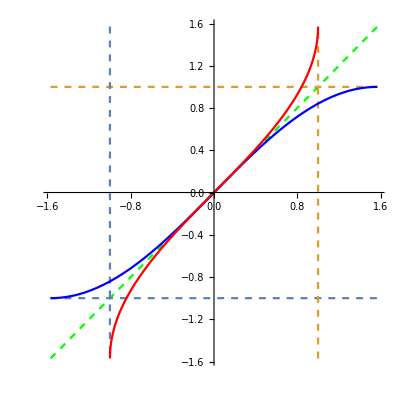

```mathematica
f1=Plot[Sin[x],{x,-Pi/2,Pi/2},PlotRange->{-Pi/2,Pi/2},AspectRatio->Automatic,PlotStyle->Blue];
f2=Plot[ArcSin[x],{x,-1,1},PlotStyle->Red];
f3=Plot[x,{x,-Pi/2,Pi/2},PlotStyle->{Green,Dashed},AspectRatio->Automatic];
f39=Plot[{-1,1},{x,-Pi/2,Pi/2},PlotStyle->Dashed];
f37=ContourPlot[{x==-1,x==1},{x,-2Pi,2Pi},{y,-Pi/2,Pi/2},ContourStyle->Dashed];
Show[f3,f39,f37,f1,f2]
```

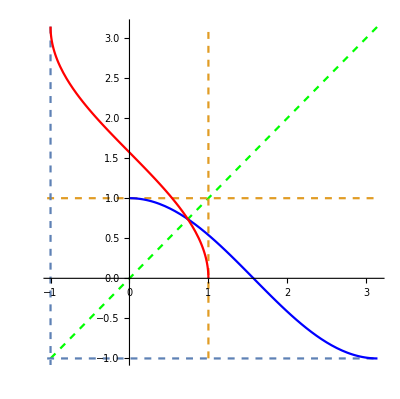

```mathematica
f4=Plot[Cos[x],{x,0,Pi},PlotRange->{-Pi/2,Pi/2},AspectRatio->Automatic,PlotStyle->Blue];
f5=Plot[ArcCos[x],{x,-1,1},PlotStyle->Red];
f6=Plot[x,{x,-1,Pi},PlotStyle->{Green,Dashed},AspectRatio->Automatic];
f69=Plot[{-1,1},{x,-Pi/2,Pi},PlotStyle->Dashed];
f67=ContourPlot[{x==-1,x==1},{x,-2Pi,2Pi},{y,-Pi/2,Pi},ContourStyle->Dashed];
Show[f6,f69,f67,f4,f5]
```

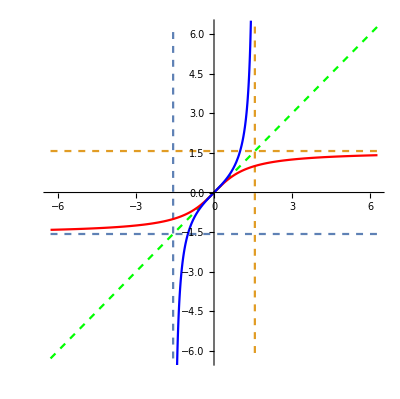

```mathematica
f7=Plot[Tan[x],{x,-0.49999Pi,0.49999Pi},PlotStyle->Blue];
f8=Plot[ArcTan[x],{x,-2Pi,2Pi},PlotStyle->Red];
f9=Plot[x,{x,-2Pi,2Pi},PlotStyle->{Green,Dashed},AspectRatio->Automatic];
f99=Plot[{-Pi/2,Pi/2},{x,-2Pi,2Pi},PlotStyle->Dashed];
f97=ContourPlot[{x==-Pi/2,x==Pi/2},{x,-2Pi,2Pi},{y,-2Pi,2Pi},ContourStyle->Dashed];
Show[f9,f99,f97,f8,f7]
```

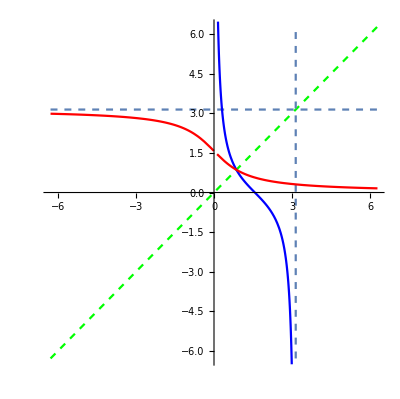

```mathematica
f10=Plot[Cot[x],{x,0.00001Pi,0.99999Pi},PlotStyle->Blue];
f11=Plot[Piecewise[{{ArcCot[x],x>0},{ArcCot[x]+Pi,x<0}}],{x,-2Pi,2Pi},PlotStyle->Red];
f12=Plot[x,{x,-2Pi,2Pi},PlotStyle->{Green,Dashed},AspectRatio->Automatic];
f109=Plot[Pi,{x,-2Pi,2Pi},PlotStyle->Dashed];
f107=ContourPlot[x==Pi,{x,-2Pi,2Pi},{y,-2Pi,2Pi},ContourStyle->Dashed];
Show[f12,f109,f107,f10,f11]
```

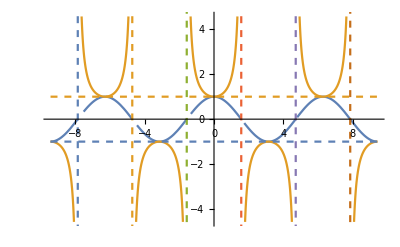

```mathematica
f111=Plot[{Cos[x],Sec[x]},{x,-3Pi,3Pi},Exclusions->Cos[x]==0];
f112=ContourPlot[{x==-2.5Pi,x==-1.5Pi,x==-0.5Pi,
x==0.5Pi,x==1.5Pi,x==2.5Pi},{x,-3Pi,3Pi},{y,-5,5},
ContourStyle->{Dashed}];
f113=Plot[{-1,1},{x,-3Pi,3Pi},PlotStyle->Dashed];
Show[f111,f112,f113]
```

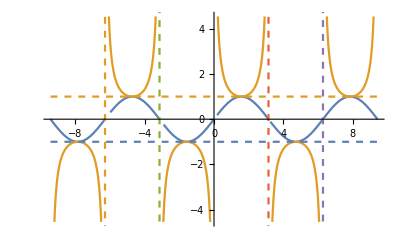

```mathematica
f121=Plot[{Sin[x],Csc[x]},{x,-3Pi,3Pi},Exclusions->Sin[x]==0];
f122=ContourPlot[{x==-3Pi,x==-2Pi,x==-Pi,
x==Pi,x==2Pi,x==3Pi},{x,-3Pi,3Pi},{y,-5,5},
ContourStyle->{Dashed}];
f123=Plot[{-1,1},{x,-3Pi,3Pi},PlotStyle->Dashed];
Show[f121,f122,f123]
```

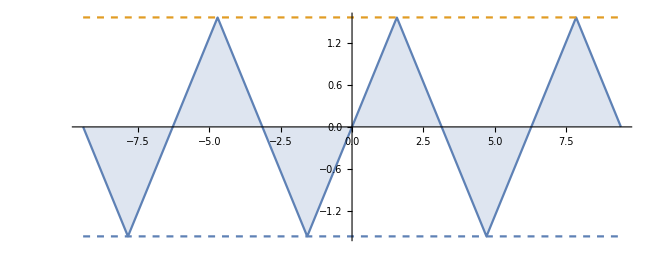

```mathematica
f131=Plot[{ArcSin[Sin[x]]},{x,-3Pi,3Pi},AspectRatio->Automatic,Filling->Axis];
f132=Plot[{-Pi/2,Pi/2},{x,-3Pi,3Pi},PlotStyle->Dashed,AspectRatio->Automatic];
Show[f131,f132]
```

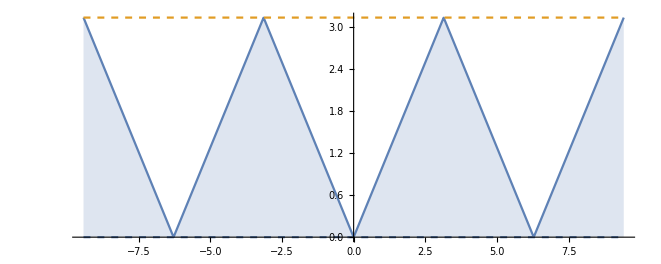

```mathematica
f141=Plot[{ArcCos[Cos[x]]},{x,-3Pi,3Pi},AspectRatio->Automatic,Filling->Axis];
f142=Plot[{0,Pi},{x,-3Pi,3Pi},PlotStyle->Dashed];
Show[f141,f142]
```

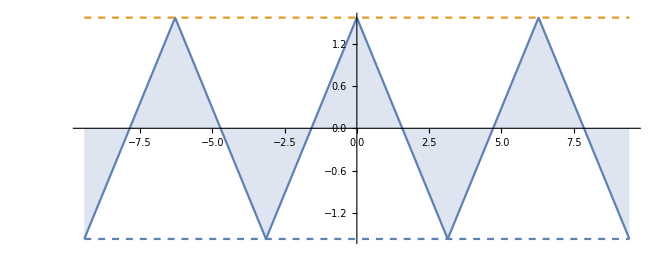

```mathematica
f151=Plot[{ArcSin[Cos[x]]},{x,-3Pi,3Pi},AspectRatio->Automatic,Filling->Axis];
f152=Plot[{-Pi/2,Pi/2},{x,-3Pi,3Pi},PlotStyle->Dashed];
Show[f151,f152]
```

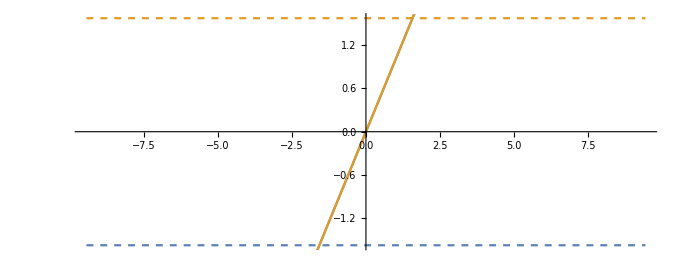

```mathematica
f161=Plot[{Cos[ArcCos[x]],Sin[ArcSin[x]]},{x,-3Pi,3Pi},AspectRatio->Automatic];
Show[f132,f161]
```

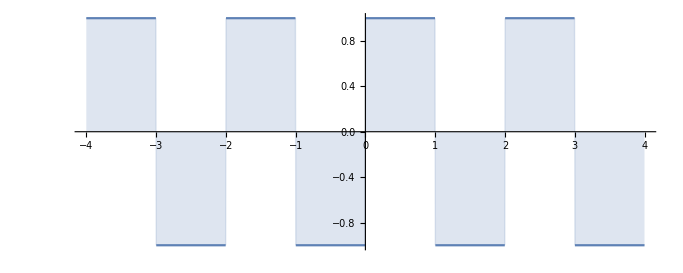

```mathematica
Plot[(-1)^(Round[x-0.5]),{x,-4,4},AspectRatio->Automatic,Filling->Axis]
```